Amy Hu
Project 1

I have not used Mathematica or Matlab before, although I have used the matplotlib in Python. I have some experience in Python, Javascript, R/RStudio, and C++. I primarily use Python, though, and have the most experience with it as well.

```mathematica
Remove["Global`*"]
(*3*)
(*i*)
a= (3.9122 * 10^2)^(1/3) (√(2.017*10^-5))/(3.661*10^-4);

(*ii*)
b = NumberForm[a, 4];

Print["3) i) ", a, "\nii) ", b]
```

3) i) 89.7209
ii) 89.72

```mathematica
Remove["Global`*"]
(*4*)
a = Factor[2 x^4 y^6+6 x^2 y^3-20];

Print["4) ", a]
```

4) 2 (-2+x^2 y^3) (5+x^2 y^3)

```mathematica
Remove["Global`*"]
(*5*)
a = Sec[θ] *Tan[θ] *(Sec[θ] + Tan[θ])+ (Sec[θ] - Tan[θ]);

Print["5) ", FullSimplify[a]]
```

5) Sec[θ]^3+Tan[θ]^3

```mathematica
Remove["Global`*"]
(*6*)
x[t_] = -500.0 + 5*10^9 t -1.5 * 10^-7 t^2;
(*i*)
t1 = (-5*10^9+ √((5*10^9)^2-4 (-1.5 * 10^-7)(-500.0)))/(2(-1.5 * 10^-7));
t2 = (-5*10^9- √((5*10^9)^2-4 (-1.5 * 10^-7)(-500.0)))/(2(-1.5 * 10^-7));

(*ii*)

v1xAvg = (x[t1] - x[0])/(t1 - 0);
v2xAvg = (x[t2] - x[0])/(t2 - 0);

(*iii*)

t1Better = -500.0/(-1.5*10^-7)/t2;

v1xBetterAvg = x[t1Better]/(t1Better - 0) - x[0]/(t1Better - 0);

Print["6) i) The object passes through the origin at t1 = ", t1, "s and t2 = ", t2, "s"]
Print["ii) The average velocity at t1 is ", v1xAvg, " and the average velocity at t2 is ", v2xAvg]
Print["iii) If we account for the loss of significance in t1, we will discover that t1 should be ", t1Better, " and the average velocity at t1 is instead ", v1xBetterAvg]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

6) i) The object passes through the origin at t1 = 0.s and t2 = 3.33333×10^16s

ii) The average velocity at t1 is Indeterminate and the average velocity at t2 is 1.5×10^-14

iii) If we account for the loss of significance in t1, we will discover that t1 should be 1.×10^-7 and the average velocity at t1 is instead 5.×10^9

```mathematica
Remove["Global`*"]
(* 7 *)
σ1 = { { 0, 1},
      {1, 0}};
σ2 = { { 0, -I},
      {I, 0}};
σ3 = { { 1, 0},
      {0, -1}};
identity = { { 1, 0},
      {0, 1}};
(* i *)
x[m_]=If[identity == m, " so it is an identity matrix", " is not an identity matrix"];
m1 = σ1.σ1;
m2 = σ2.σ2;
m3 = σ3.σ3;
m4 = -I*σ1.σ2.σ3;

Print["7) i)"]
Print ["σ1^2 = ", MatrixForm[m1], x[m1]]
Print ["σ2^2 = ", MatrixForm[m2], x[m2]]
Print ["σ3^2 = ", MatrixForm[m3], x[m3]]
Print ["-iσ1σ2σ3 = ", MatrixForm[m4], x[m4]]

(* ii *)
a = σ1.σ2 - σ2.σ1;
b = 2I*σ3;
y[m_, n_] = If [a==b," = ", " ≠ " ];
Print["ii)"]
Print["σ1σ2 - σ2σ1 = ", MatrixForm[a], y[a, b], MatrixForm[b], " = 2iσ3"]
```

7) i)

σ1^2 = (1 | 0
0 | 1) so it is an identity matrix

σ2^2 = (1 | 0
0 | 1) so it is an identity matrix

σ3^2 = (1 | 0
0 | 1) so it is an identity matrix

-iσ1σ2σ3 = (1 | 0
0 | 1) so it is an identity matrix

ii)

σ1σ2 - σ2σ1 = (2 ⅈ | 0
0 | -2 ⅈ) = (2 ⅈ | 0
0 | -2 ⅈ) = 2iσ3

8)i)

The velocity vector is {Cos[π/6+t]+t (Sin[t]-Sin[π/6+t]),-t Cos[t]+t Cos[π/6+t]+Sin[π/6+t]}

The acceleration vector is {t Cos[t]-t Cos[π/6+t]+Sin[t]-2 Sin[π/6+t],-Cos[t]+2 Cos[π/6+t]+t (Sin[t]-Sin[π/6+t])}

The speed as at any time t is √(1-t (1+(-2+√3) t))

ii) The angle in radians between the acceleration and velocity is about 1.0626. The exact angle is ArcCos[√(317/1924+(20 √3)/481)]

iii)

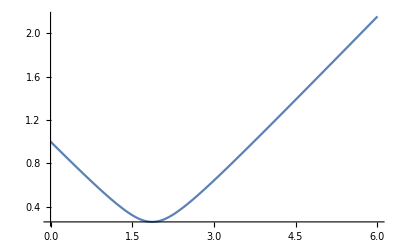

iv)

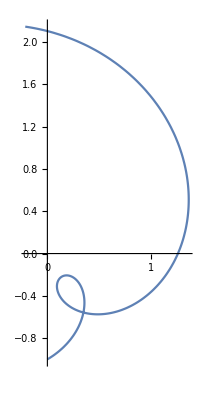

```mathematica
Remove["Global`*"]
(* 8 *)
(* i *)
r[t_] = {Sin[t]-t Cos[t]+ t Cos[t+π/6], t Sin[t+π/6]-t Sin[t]-Cos[t]};
v[t_]= FullSimplify[D[r[t], t]];
a[t_]= FullSimplify[D[r[t], {t, 2}]];

speed[t_] =√((v[t][[1]])^2 + (v[t][[2]])^2) //FullSimplify;
accelMagnitude[t_] = √((a[t][[1]])^2+ (a[t][[2]])^2) //FullSimplify;

(* ii *)
dotproduct = v[3].a[3] //FullSimplify;
magproduct = speed[3]*accelMagnitude[3] //FullSimplify;
b=dotproduct/magproduct//FullSimplify;
θ = NumberForm[ArcCos[1.0 * b], 5];

(* iii *)
tlo = 0;
thi = 6;
plot1= Plot[speed[t], {t, tlo, thi}];

(* iv *)

traj = ParametricPlot[r[t], {t, tlo, thi}];

Print["8)i)"]
Print["The velocity vector is ", v[t]]
Print["The acceleration vector is ", a[t]]
Print["The speed as at any time t is ", speed[t]]
Print["ii) The angle in radians between the acceleration and velocity is about ", θ, ". The exact angle is ", ArcCos[b]]
Print["iii) "]
Print[plot1]
Print["iv) "]
Print[traj]
```